# Solving k-essence background evolution ODE

## Parameters

```mathematica
Xhat=8;
g0=0.0;
g2=1.0;
g4=1 10^-12;
```

## Definitions:

```mathematica
X = 1/(2 a[τ]^2)(ϕ'[τ]^2-(D[ϕ[τ], x])^2);
K = -g0+g2(X-Xhat)^2+g4(X-Xhat)^4;
Subscript[K, X]=2.0g2(X-Xhat)+4.0g4(X-Xhat)^3;
Subscript[K, XX] = 2 g2 +12 g4 (X-Xhat)^2;
Subscript[K, ϕ]=0;
Subscript[K, ϕX]=0;
cs2 = Subscript[K, X]/(2X Subscript[K, XX]+Subscript[K, X]);
```

0

## Functions

```mathematica
scalfactor[z_]:=1/(1+z);
redshift[a_]:=1/a-1;
(*Function to compute conformal time for a given redshift*)
tau[zs_,H0_,Ωm_,Ωd_,w_,Ωr_]:=NIntegrate[H0^-1/(√(Ωd(1+z)^(3(1+w)) +Ωm (1+z)^3+Ωr(1+z)^4)),{z,zs,∞},PrecisionGoal->12,AccuracyGoal->12]
(*Conformal Hubble Function at a given redshift *)
ConformalHubble[z_,H0_,Ωm_,Ωd_,w_,Ωr_]:=H0 √(Ωd(1+z)^(1+3 w) +Ωm (1+z)+Ωr(1+z)^2)
```

## Cosmological components

```mathematica
w = -1.0;
H0=0.0691023;
Ωm=0.31;
ΩR=9 10^-5;
Ωd=1-Ωm-ΩR;
```

## ODEs

```mathematica
ODE = (Subscript[K, X]+ ϕ'[τ]^2/a[τ]^2 Subscript[K, XX])ϕ''[τ] - a[τ]^2(Subscript[K, ϕ] - ϕ'[τ]^2/a[τ]^2 Subscript[K, ϕX]) - a'[τ]/a[τ](2 Subscript[K, X] -  ϕ'[τ]^2/a[τ]^2 Subscript[K, XX])ϕ'[τ] + Subscript[K, X] D[ϕ[τ], x,x] + Subscript[K, ϕX] D[ϕ[τ], x]D[ϕ[τ], x] +2 Subscript[K, XX]/a[τ]^2 ϕ'[τ]D[ϕ[τ], x]D[ϕ[τ], x,τ]- a'[τ]/a[τ] Subscript[K, XX]/a[τ]^2 ϕ'[τ]D[ϕ[τ], x]D[ϕ[τ], x]- Subscript[K, XX]/a[τ]^2 D[ϕ[τ], x]D[ϕ[τ], x] D[ϕ[τ], x,x];
ODEa = a'[τ] -a[τ]H0 √(ΩR a[τ]^-2 + Ωm a[τ]^-1+(1-Ωm)a[τ]^(-(1+3 w)));
```

## Initial conditions

```mathematica
τini = tau[100,H0,Ωm,Ωd,w,ΩR];
τfin= tau[0,H0,Ωm,Ωd,w,ΩR];
```

## ODEs solution

```mathematica
s=NDSolve[{ODEa==0,ODE==0,a[τfin]==1.0,ϕ[τini]==10^-7, ϕ'[τini]==10^-9},{a[τ],a'[τ],ϕ[τ],ϕ'[τ]},{τ,τini,τfin}]
```

{{a[τ]→InterpolatingFunction[…][τ],a'[τ]→InterpolatingFunction[…][τ],ϕ[τ]→InterpolatingFunction[…][τ],ϕ'[τ]→InterpolatingFunction[…][τ]}}

## Figures

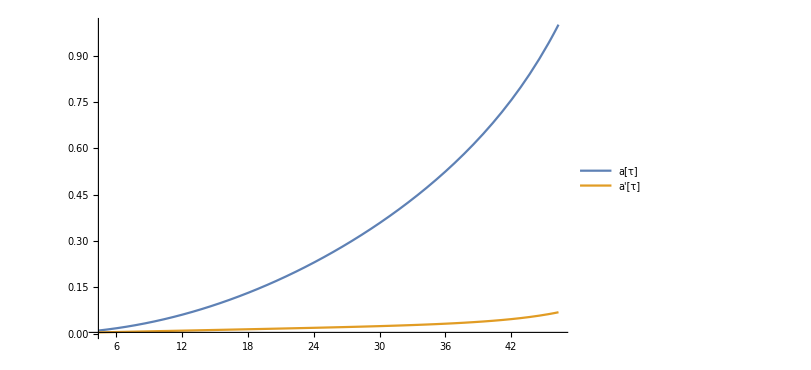

```mathematica
plt = Plot[Evaluate[{a[τ],a'[τ]}/.s],{τ,τini,τfin},PlotRange->Full,PlotLegends->{"a[τ]","a'[τ]"}, PlotStyle->Thick, ImageSize->600]
```

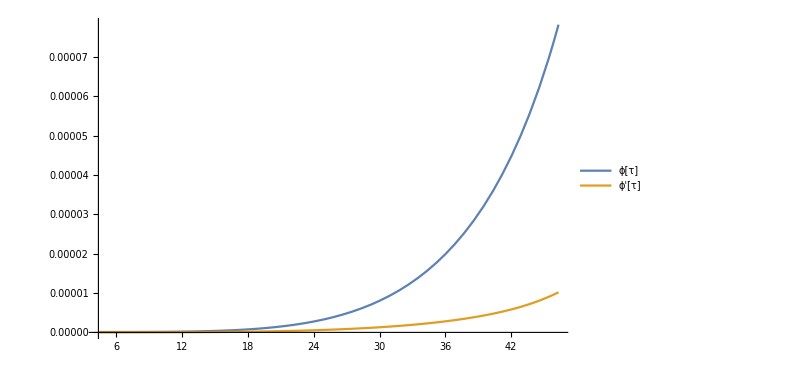

```mathematica
plt2 = Plot[Evaluate[{ϕ[τ],ϕ'[τ]}/.s],{τ,τini,τfin},PlotRange->Full,PlotLegends->{"ϕ[τ]","ϕ'[τ]"}, PlotStyle->Thick, ImageSize->600]
```